# xPand Benchmarking

## Set up

```mathematica
SetDirectory["~/CMB"];
```

```mathematica
Block[{Print},
<<xAct/xPand.m;
]
$DefInfoQ=False;
SetOptions[AutomaticRules,Verbose->False];
```

We define the manifold, the metric and the slicing

```mathematica
(*DefConstantSymbol[d];*)
DefManifold[M,4(*d*),{α,β,γ,μ,ν,λ,σ}];
DefMetric[-1,g[-α,-β],CD,{";","OverBar[∇]"},PrintAs->"ḡ"];
SetSlicing[g,nM,hM,cdM,{"|","D̄"},"Minkowski"];
SetSlicing[g,n,h,cd,{"|","D̄"},"FLFlat"];
SetSlicing[g,n2,h2,cd2,{"|","D̄"},"FLCurved"];
SetSlicing[g,n3,h3,cd3,{"|","D̄"},"BianchiI"];
SetSlicing[g,n4,h4,cd4,{"|","D̄"},"BianchiB"];
```

** DefMetric: Don't know yet how to define epsilon for a frozen metric.

** MakeRule: Potential problems moving indices on the LHS.

** DefMetric: Don't know yet how to define epsilon for a frozen metric.

** MakeRule: Potential problems moving indices on the LHS.

** DefMetric: Don't know yet how to define epsilon for a frozen metric.

** MakeRule: Potential problems moving indices on the LHS.

** DefMetric: Don't know yet how to define epsilon for a frozen metric.

** MakeRule: Potential problems moving indices on the LHS.

These commands are necessary, but if they are forgotten, they are automatically called. So for a minimal example we do not evaluate them

```mathematica
DefMetricFields[g,dg,hM]
DefMatterFields[uf, duf,hM]

DefMetricFields[g,dg,h]
DefMatterFields[uf, duf,h]

DefMetricFields[g,dg,h2]
DefMatterFields[uf, duf,h2]

DefMetricFields[g,dg,h3]
DefMatterFields[uf, duf,h3]

DefMetricFields[g,dg,h4]
DefMatterFields[uf, duf,h4]
```

The Hubble factor  has to be introduced from the scale factor.

## Benchmark

```mathematica
MyxPandBenchMark[expr_,h_,order_,gauge_]:=ToxPand[expr,dg,uf,duf,h, gauge, order]
```

```mathematica
ordermax=4
```

4

```mathematica
$OpenConstantsOfStructure=False;
```

```mathematica
TimingsxPert=Table[{i,First@AbsoluteTiming[ExpandPerturbation@Perturbed[Conformal[g,gah42][RicciScalarCD[]],i]//ContractMetric//ToCanonical]},{i,1,ordermax}]
```

{{1,0.18519},{2,0.612822},{3,2.50299},{4,13.95967}}

```mathematica
TimingsMinkowski=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],hM,i,"NewtonGauge"]]},{i,1,ordermax}]
TimingsMinkowskiSynchronous=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],hM,i,"SynchronousGauge"]]},{i,1,ordermax}]
TimingsMinkowskiFlat=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],hM,i,"FlatGauge"]]},{i,1,ordermax}]
TimingsMinkowskiComoving=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],hM,i,"ComovingGauge"]]},{i,1,ordermax}]
TimingsMinkowskiAny=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],hM,i,"AnyGauge"]]},{i,1,ordermax}]
```

{{1,1.55152},{2,7.00197}}

{{1,1.49325},{2,12.95898}}

{{1,1.22823},{2,6.72454}}

{{1,1.34463},{2,7.87932}}

{{1,1.59435},{2,17.14754}}

```mathematica
TimingsFLFlat=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h,i,"NewtonGauge"]]},{i,1,ordermax}]
TimingsFLFlatSynchronous=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h,i,"SynchronousGauge"]]},{i,1,ordermax}]
TimingsFLFlatFlat=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h,i,"FlatGauge"]]},{i,1,ordermax}]
TimingsFLFlatComoving=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h,i,"ComovingGauge"]]},{i,1,ordermax}]
TimingsFLFlatAny=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h,i,"AnyGauge"]]},{i,1,ordermax}]
```

{{1,1.67365},{2,9.799575}}

{{1,1.97795},{2,17.95158}}

{{1,1.76446},{2,10.78325}}

{{1,1.81529},{2,12.09808}}

{{1,2.14007},{2,23.87603}}

```mathematica
TimingsFLCurved=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h2,i,"NewtonGauge"]]},{i,1,ordermax}]
TimingsFLCurvedSynchronous=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h2,i,"SynchronousGauge"]]},{i,1,ordermax}]
TimingsFLCurvedFlat=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h2,i,"FlatGauge"]]},{i,1,ordermax}]
TimingsFLCurvedComoving=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h2,i,"ComovingGauge"]]},{i,1,ordermax}]
TimingsFLCurvedAny=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h2,i,"AnyGauge"]]},{i,1,ordermax-1}]
```

{{1,1.7894},{2,10.08922}}

{{1,2.13666},{2,23.67044}}

{{1,1.80393},{2,11.49158}}

{{1,1.9866},{2,13.16532}}

{{1,2.94446}}

```mathematica
TimingsBianchiI=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h3,i,"NewtonGauge"]]},{i,1,ordermax}]
TimingsBianchiISynchronous=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h3,i,"SynchronousGauge"]]},{i,1,ordermax}]
TimingsBianchiIFlat=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h3,i,"FlatGauge"]]},{i,1,ordermax}]
TimingsBianchiIComoving=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h3,i,"ComovingGauge"]]},{i,1,ordermax}]
TimingsBianchiIAny=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h3,i,"AnyGauge"]]},{i,1,ordermax-1}]
```

{{1,6.2098},{2,44.70285}}

{{1,8.2332},{2,74.6605}}

{{1,5.29351},{2,35.80599}}

{{1,6.60827},{2,49.13049}}

{{1,9.15736}}

```mathematica
TimingsBianchiB=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h4,i,"NewtonGauge"]]},{i,1,ordermax-1}]
TimingsBianchiBSynchronous=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h4,i,"SynchronousGauge"]]},{i,1,ordermax-2}]
TimingsBianchiBFlat=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h4,i,"FlatGauge"]]},{i,1,ordermax-1}]
TimingsBianchiBComoving=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h4,i,"ComovingGauge"]]},{i,1,ordermax-1}]
TimingsBianchiBAny=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h4,i,"AnyGauge"]]},{i,1,ordermax-2}]
```

{{1,15.86126}}

{{1,20.98295}}

{{1,10.11119}}

{{1,14.46671}}

{}

## Saving results and Plots

Just to have an idea of the ratio of timings between succesive orders. We clearly see that it is an approximate power law.

```mathematica
FirstTime=True;
```

```mathematica
NameFileNewt=StringJoin["SaveTimingsNewtonGauge",ToString[ordermax],".dat"];
If[FirstTime,
Put[{TimingsxPert,TimingsMinkowski,TimingsFLFlat,TimingsFLCurved,TimingsBianchiI,TimingsBianchiB},NameFileNewt];,{TimingsxPert,TimingsMinkowski,TimingsFLFlat,TimingsFLCurved,TimingsBianchiI,TimingsBianchiB}=Get[NameFileNewt]]


NameFileSynchronous=StringJoin["SaveTimingsSynchronousGauge",ToString[ordermax],".dat"];
If[FirstTime,
Put[{TimingsxPert,TimingsMinkowskiSynchronous,TimingsFLFlatSynchronous,TimingsFLCurvedSynchronous,TimingsBianchiISynchronous,TimingsBianchiBSynchronous},NameFileSynchronous];,{TimingsxPert,TimingsMinkowskiSynchronous,TimingsFLFlatSynchronous,TimingsFLCurvedSynchronous,TimingsBianchiISynchronous,TimingsBianchiBSynchronous}=Get[NameFileSynchronous]]

NameFileFlat=StringJoin["SaveTimingsFlatGauge",ToString[ordermax],".dat"];
If[FirstTime,
Put[{TimingsxPert,TimingsMinkowskiFlat,TimingsFLFlatFlat,TimingsFLCurvedFlat,TimingsBianchiIFlat,TimingsBianchiBFlat},NameFileFlat];,{TimingsxPert,TimingsMinkowskiFlat,TimingsFLFlatFlat,TimingsFLCurvedFlat,TimingsBianchiIFlat,TimingsBianchiBFlat}=Get[NameFileFlat]]


NameFileComoving=StringJoin["SaveTimingsComovingGauge",ToString[ordermax],".dat"];
If[FirstTime,
Put[{TimingsxPert,TimingsMinkowskiComoving,TimingsFLFlatComoving,TimingsFLCurvedComoving,TimingsBianchiIComoving,TimingsBianchiBComoving},NameFileComoving];,{TimingsxPert,TimingsMinkowskiComoving,TimingsFLFlatComoving,TimingsFLCurvedComoving,TimingsBianchiIComoving,TimingsBianchiBComoving}=Get[NameFileComoving]]
```

```mathematica
NameFileAny=StringJoin["SaveTimingsAnyGauge",ToString[ordermax],".dat"];
If[FirstTime,
Put[{TimingsxPert,TimingsMinkowskiAny,TimingsFLFlatAny,TimingsFLCurvedAny,TimingsBianchiIAny,TimingsBianchiBAny},NameFileAny];,{TimingsxPert,TimingsMinkowskiAny,TimingsFLFlatAny,TimingsFLCurvedAny,TimingsBianchiIAny,TimingsBianchiBAny}=Get[NameFileAny]]
```

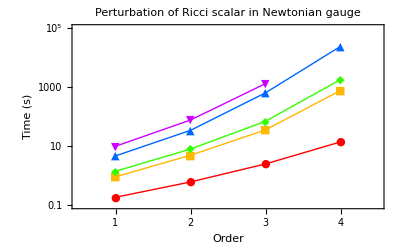

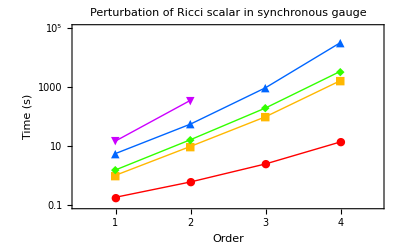

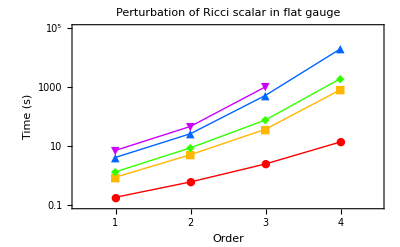

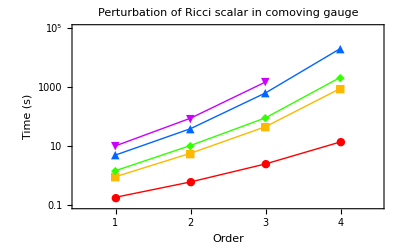

```mathematica
plotnewt=ListLogPlot[{TimingsxPert,TimingsMinkowski,(*TimingsFLFlat,*)TimingsFLCurved,TimingsBianchiI,TimingsBianchiB},Frame->True,FrameLabel->{Style["Order",12],Style["Time (s)",12]},PlotRange->{{0.5,ordermax+0.5},{.1,100000}},PlotLabel->Style["Perturbation of Ricci scalar in Newtonian gauge",12],PlotMarkers->{Automatic,Medium},FrameStyle->{{Thickness[.0035],Thickness[.0035]},{Thickness[.0035],Thickness[.0035]}},Joined->True,PlotStyle->{Hue[0],Hue[0.12],Hue[0.3],Hue[0.6],Hue[0.8],Hue[0.9]},FrameTicks->{{Automatic,None},{Range[ordermax],None}}]

plotsync=ListLogPlot[{TimingsxPert,TimingsMinkowskiSynchronous,(*TimingsFLFlat,*)TimingsFLCurvedSynchronous,TimingsBianchiISynchronous,TimingsBianchiBSynchronous},Frame->True,FrameLabel->{Style["Order",12],Style["Time (s)",12]},PlotRange->{{0.5,ordermax+0.5},{.1,100000}},PlotLabel->Style["Perturbation of Ricci scalar in synchronous gauge",12],PlotMarkers->{Automatic,Medium},FrameStyle->{{Thickness[.0035],Thickness[.0035]},{Thickness[.0035],Thickness[.0035]}},Joined->True,PlotStyle->{Hue[0],Hue[0.12],Hue[0.3],Hue[0.6],Hue[0.8],Hue[0.9]},FrameTicks->{{Automatic,None},{Range[ordermax],None}}]

plotflat=ListLogPlot[{TimingsxPert,TimingsMinkowskiFlat,(*TimingsFLFlat,*)TimingsFLCurvedFlat,TimingsBianchiIFlat,TimingsBianchiBFlat},Frame->True,FrameLabel->{Style["Order",12],Style["Time (s)",12]},PlotRange->{{0.5,ordermax+0.5},{.1,100000}},PlotLabel->Style["Perturbation of Ricci scalar in flat gauge",12],PlotMarkers->{Automatic,Medium},FrameStyle->{{Thickness[.0035],Thickness[.0035]},{Thickness[.0035],Thickness[.0035]}},Joined->True,PlotStyle->{Hue[0],Hue[0.12],Hue[0.3],Hue[0.6],Hue[0.8],Hue[0.9]},FrameTicks->{{Automatic,None},{Range[ordermax],None}}]

plotcom=ListLogPlot[{TimingsxPert,TimingsMinkowskiComoving,(*TimingsFLFlat,*)TimingsFLCurvedComoving,TimingsBianchiIComoving,TimingsBianchiBComoving},Frame->True,FrameLabel->{Style["Order",12],Style["Time (s)",12]},PlotRange->{{0.5,ordermax+0.5},{.1,100000}},PlotLabel->Style["Perturbation of Ricci scalar in comoving gauge",12],PlotMarkers->{Automatic,Medium},FrameStyle->{{Thickness[.0035],Thickness[.0035]},{Thickness[.0035],Thickness[.0035]}},Joined->True,PlotStyle->{Hue[0],Hue[0.12],Hue[0.3],Hue[0.6],Hue[0.8],Hue[0.9]},FrameTicks->{{Automatic,None},{Range[ordermax],None}}]
```

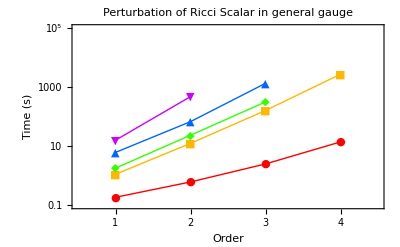

```mathematica
plotany=ListLogPlot[{TimingsxPert,TimingsMinkowskiAny,(*TimingsFLFlatAny,*)TimingsFLCurvedAny,TimingsBianchiIAny,TimingsBianchiBAny},Frame->True,FrameLabel->{Style["Order",12],Style["Time (s)",12]},PlotRange->{{0.5,ordermax+0.5},{.1,100000}},PlotLabel->Style["Perturbation of Ricci Scalar in general gauge",12],PlotMarkers->{Automatic,Medium},FrameStyle->{{Thickness[.0035],Thickness[.0035]},{Thickness[.0035],Thickness[.0035]}},Joined->True,PlotStyle->{Hue[0],Hue[0.12],Hue[0.3],Hue[0.6],Hue[0.8]},FrameTicks->{{Automatic,None},{Range[ordermax],None}}]
```

```mathematica
Export["TimingNewtonGauge.pdf",plotnewt,"pdf"];
Export["TimingNewtonGauge.eps",plotnewt,"eps"];

Export["TimingSynchronousGauge.pdf",plotsync,"pdf"];
Export["TimingSynchronousGauge.eps",plotsync,"eps"];

Export["TimingFlatGauge.pdf",plotflat,"pdf"];
Export["TimingFlatGauge.eps",plotflat,"eps"];

Export["TimingComovingGauge.pdf",plotcom,"pdf"];
Export["TimingComovingGauge.eps",plotcom,"eps"];
```

```mathematica
Export["TimingAnyGauge.pdf",plotany,"pdf"];
Export["TimingAnyGauge.eps",plotany,"eps"];
```